```mathematica
$Assumptions={m>0&&m<1&&ϕ>-Pi/2&&ϕ<Pi/2};
```

```mathematica
(*δχ from Eq.(67) of 2502.03929*)
δχ[ϕ_]=δχav - δχdiff (1 - 2 Sin[ϕ]^2);
(*Input simplified values of <δχ^n>*)
f1[m_]=2/m(EllipticE[m]/EllipticK[m]-1+m/2);
f2[m_]=4/m^2((EllipticE[m]/EllipticK[m])^2+2/3 EllipticE[m]/EllipticK[m](m-2)+m^2/8-m/3+1/3);
f3[m_]=16/m^3((EllipticE[m]/EllipticK[m])^3+(EllipticE[m]/EllipticK[m])^2 (m-2)+EllipticE[m]/EllipticK[m] ((4 m^2)/15-(19 m)/15+19/15)-(2 m^2)/15+(2 m)/5-4/15);
δχprecavg[m_]=δχav-f1[m]δχdiff;
δχ2precavg[m_]=δχprecavg[m]^2+(1/2-f2[m])δχdiff^2;
δχ3precavg[m_]=δχprecavg[m](3δχ2precavg[m]-2 δχprecavg[m]^2)-f3[m] δχdiff^3;
(*Compute of Eq.(77) for δχ^n*)
δχint[m_,ϕ_]=Integrate[δχ[ϕ]/(√(1-m Sin[ϕ]^2)),ϕ];
δχ2int[m_,ϕ_]=Integrate[δχ[ϕ]^2/(√(1-m Sin[ϕ]^2)),ϕ];
δχ3int[m_,ϕ_]=Integrate[δχ[ϕ]^3/(√(1-m Sin[ϕ]^2)),ϕ];
(*Compare with <δχ^n> computed from Eq.(77)*)
Simplify[δχprecavg[m]-(δχint[m,Pi/2]-δχint[m,-Pi/2])/(2EllipticK[m])]
Simplify[δχ2precavg[m]-(δχ2int[m,Pi/2]-δχ2int[m,-Pi/2])/(2EllipticK[m])]
Simplify[δχ3precavg[m]-(δχ3int[m,Pi/2]-δχ3int[m,-Pi/2])/(2EllipticK[m])]
```

0

0

0

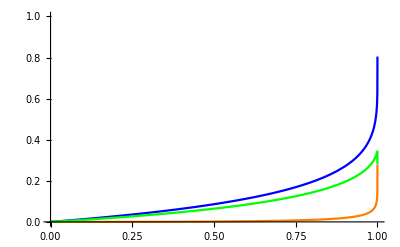

```mathematica
(*Plot the different functions of m that appear*)
Plot[{-f1[m],f2[m],f3[m]},{m,0,1},PlotRange->{0,1},PlotStyle->{Blue,Orange,Green}]
```

```mathematica
(*Compute small m series of the different functions of m that appear*)
Series[f1[m],{m,0,5}]
Series[f2[m],{m,0,5}]
Series[32/(3m)f3[m],{m,0,5}]
```

-m/8-m^2/16-(41 m^3)/1024-(59 m^4)/2048-(727 m^5)/32768+O[m]^6

m^2/256+m^3/256+(29 m^4)/8192+(13 m^5)/4096+O[m]^6

1+m/2+(5 m^2)/16+(7 m^3)/32+(5375 m^4)/32768+(8443 m^5)/65536+O[m]^6

```mathematica
(*compute combination of <δχ> and <δχ^2> that best approximates <δχ^3>*)
Simplify[Series[(δχ3precavg[m]-(δχprecavg[m](a δχ2precavg[m]+(1-a)δχprecavg[m]^2)))/δχdiff^2,{m,0,4}]]
```

-1/2 (-3+a) δχav+1/32 (3-2 a) δχdiff m+1/256 ((-3+a) δχav+4 (3-2 a) δχdiff) m^2+1/512 (2 (-3+a) δχav+5 (3-2 a) δχdiff) m^3+((29 (-3+a) δχav+56 (3-2 a) δχdiff) m^4)/8192+O[m]^5